```mathematica
Series[DiracDelta[x],{x,0,5}]
```

DiracDelta[0]+DiracDelta'[0] x+1/2 DiracDelta''[0] x^2+1/6 DiracDelta^(3)[0] x^3+1/24 DiracDelta^(4)[0] x^4+1/120 DiracDelta^(5)[0] x^5+O[x]^6

```mathematica
FourierTransform[DiracDelta[x],x,j]
```

1/(√(2 π))

```mathematica
inner3D := 2 Pi Integrate[Exp[-2 Pi I k r Cos[θ]]*Sin[θ],{θ,0,Pi}]
```

```mathematica
Assuming[{a>0, k>0},Integrate[((3/(4Pi))/(r^2 + a^2)^(5/2))*inner3D*r^2, {r,0,Infinity}]]
```

(2 k π BesselK[1,2 a k π])/a

```mathematica
FullSimplify[Series[Out[22],{a,0,3}]]
```

Floor[-(-π+Arg[a]+Arg[k])/(2 π)] (4 ⅈ k^2 π^3+2 ⅈ k^4 π^5 a^2+O[a]^3)+(1/a^2+k^2 π^2 (-1+2 EulerGamma+2 (Log[a]+Log[k π]))+1/4 k^4 π^4 (-5+4 EulerGamma+4 Log[a]+4 Log[k π]) a^2+O[a]^3)

```mathematica
D[1/r,r]
```

-1/r^2

```mathematica
D[1/r,r]
```

-1/r^2

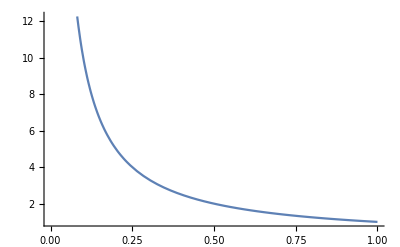

```mathematica
Plot[1/r,{r,0,1}]
```

```mathematica
Integrate[1/r^2,{r,-1,1}]
```

Integrate::idiv: Integral of 1/r^2 does not converge on {-1, 1}.

∫_-1^1 1/r^2 ⅆr

```mathematica
Integrate[1/Sqrt[x^2+y^2+z^2],{x,-1,1},{y,-1,1},{z,-1,1}]
```

-2 (π+Log[64]-12 Log[1+√3])

```mathematica
Out[11]*1.0
```

9.52031

```mathematica
Integrate[1/r*r^2 Sin[p],{p,0,Pi},{t,0,2Pi},{r,0,1.24}]
```

9.66103

```mathematica
rr=Range[1/30,1,1/30]
```

{1/30,1/15,1/10,2/15,1/6,1/5,7/30,4/15,3/10,1/3,11/30,2/5,13/30,7/15,1/2,8/15,17/30,3/5,19/30,2/3,7/10,11/15,23/30,4/5,5/6,13/15,9/10,14/15,29/30,1}

```mathematica
T=Table[{rr[[i]],1/rr[[i]]},{i,1,30}]
```

{{1/30,30},{1/15,15},{1/10,10},{2/15,15/2},{1/6,6},{1/5,5},{7/30,30/7},{4/15,15/4},{3/10,10/3},{1/3,3},{11/30,30/11},{2/5,5/2},{13/30,30/13},{7/15,15/7},{1/2,2},{8/15,15/8},{17/30,30/17},{3/5,5/3},{19/30,30/19},{2/3,3/2},{7/10,10/7},{11/15,15/11},{23/30,30/23},{4/5,5/4},{5/6,6/5},{13/15,15/13},{9/10,10/9},{14/15,15/14},{29/30,30/29},{1,1}}

```mathematica
IP:=InterpolatingPolynomial[T,x]
```

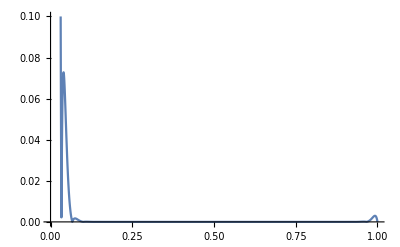

```mathematica
Plot[Abs[IP-1/x],{x,0,1},PlotRange->{0,0.1}]
```